# Time Series Forecast and Analysis

Kyle MacLaury
Riccardo Di Virgilio

## What I accomplished

I created a pipeline capable of taking time series data from a CSV and transforming it into data that can be analyzed with TimeSeriesForecasts, Linear Regression, NonLinear Regression and Machine Learning.

## What I learned

Time series forecasting is hard, particularly when the data has complex features, and you haven’t done statistical analysis in over a decade.

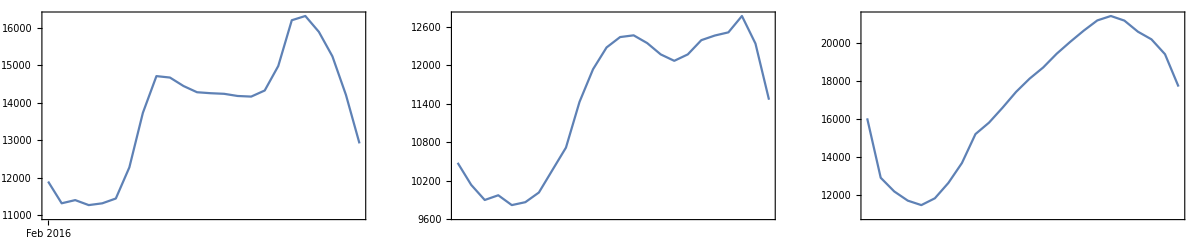

```mathematica
GraphicsRow[{
	DateListPlot[TimeSeriesWindow[resampledNEISOLoad,{DateObject[{2016,2,1}],DateObject[{2016,2,1}]}]
],
	DateListPlot[TimeSeriesWindow[resampledNEISOLoad,{DateObject[{2016,5,21}],DateObject[{2016,5,21}]}]
],
	DateListPlot[TimeSeriesWindow[resampledNEISOLoad,{DateObject[{2016,7,21}],DateObject[{2016,7,21}]}]
]
}]
```

## Analyses

### TimeSeriesForecast

The Wolfram Language has built in functions for generating TimeSeriesModels, those models can be used to generate TimeSeriesForecasts.  These functions evaluate multiple time series models, and return the evaluated model with the highest explanatory value.  As we will see, this automatic evaluation of multiple models does not guarantee that the model returned is the best possible model to describe the data.

#### TimeSeriesModelFit

```mathematica
loadTSModel=TimeSeriesModelFit[resampledNEISOLoad]
```

TimeSeriesModel[…]

```mathematica
loadTSModelforecast=TimeSeriesForecast[loadTSModel,{72}]
```

TemporalData[…]

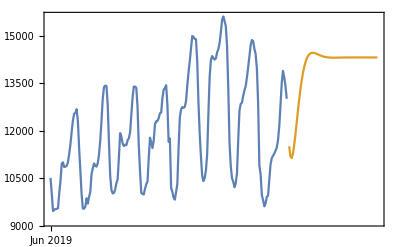

```mathematica
tsmodelDLP=DateListPlot[{
	TimeSeriesWindow[
	resampledNEISOLoad,
	{DateObject[{2019,6,1}],
	DateObject[{2019,6,8}]}],loadTSModelforecast}]
```

#### TimeSeriesForecast specifying SARIMA with Automatic Options

```mathematica
tsmodelSARIMA=TimeSeriesModelFit[resampledNEISOLoad,{"SARIMA",{Automatic,Automatic,Automatic}}]
```

TimeSeriesModel[…]

```mathematica
loadTSModelforecastSARIMA=TimeSeriesForecast[tsmodelSARIMA,{72}]
```

TemporalData[…]

```mathematica
tsmodelDLPSARIMA=DateListPlot[{
	TimeSeriesWindow[
	resampledNEISOLoad,
	{DateObject[{2019,6,1}],
	DateObject[{2019,6,8}]}],loadTSModelforecastSARIMA}]
```

-Graphics-

#### TimeSeriesForecast specifying SARIMA with Specified Options

```mathematica
tsmodelSARIMASpecified=TimeSeriesModelFit[resampledNEISOLoad,{"SARIMA",{{1,1,1},{1,1,1},24}}]
```

TimeSeriesModel[…]

```mathematica
loadTSModelforecastSARIMASpecified=TimeSeriesForecast[tsmodelSARIMASpecified,{72}]
```

TemporalData[…]

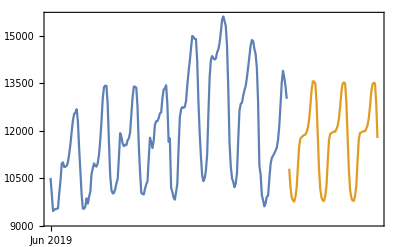

```mathematica
tsmodelDLPSARIMASpecified=DateListPlot[{
	TimeSeriesWindow[
	resampledNEISOLoad,
	{DateObject[{2019,6,1}],
	DateObject[{2019,6,8}]}],loadTSModelforecastSARIMASpecified}]
```

Many thanks to Riccardo, Tuseeta and Bob Nachbar for  their guidance.